# Axon Image Processing

Analysis of axon expression intensity in the neocortex

Jihyeon Je, Jun. 24,  2018

Write a 3-5 sentence basic introduction of the topic, particularly why it’s interesting. Note that the title should be as straightforward as possible (Rhythmic Timelines, not: Sonifying Clave son – Exploring Musical Rhythm), so the introduction provides the opportunity to elaborate and engage the reader. Don’t make the subjects overly general—have them match the specificity of the content.

## Background

The neocortex, also called the neopallium and isocortex, is the part of the mammalian brain involved in higher-order brain functions such as sensory perception, cognition, generation of motor commands, spatial reasoning and language. In the human brain, the neocortex is the largest part of the cerebral cortex which is the outer layer of the cerebrum, with the allocortex making up the rest. The neocortex is made up of six layers, labelled from the outermost inwards, I to VI. 

	In the adult brain, structural plasticity with synapse formation and elimination is thought to underlie aspects of long-term memory formation (Bailey and Kandel, 1993). In sparse neural networks, such as the neocortex, the extent of structural plasticity is a fundamental constraint on the memory capacity of the brain (Chklovskii et al., 2004). Plasticity over longer distances means that a larger number of neural circuits can be achieved and implies a larger memory capacity per synapse. Moreover, structural plasticity may be critical for functional recovery upon injury in the adult central nervous system (Fawcett and Geller, 1998, Chen et al., 2002, Papadopoulos, 2002). 
	
	Even less is known about the dynamics of cortical axons in the adult brain. Axons span many millimeters of cortical territory, and individual axons can target diverse areas (Zhang and Deschenes, 1998). Long-range growth of axons could therefore have a big impact on circuit plasticity. Understanding the repertoire of axonal structural changes is therefore fundamental to the mechanisms of functional rewiring in the adult brain.

	For this project, two-photon(2P) micro scoped images of distinct identified axonal arbors in the intact adult barrel cortex of GFP transgenic mice was used.

## Import Images

In order to carry out an image analysis on microscoped images, actual sizes of each pixel are needed for accurate volume and density calculations.

#### Input Pixel Sizes

Assign pixel sizes:

```mathematica
xpixelsize = 512 Quantity[, "Micrometers"];
ypixelsize = 512 Quantity[, "Micrometers"];
zstepsize = 293 Quantity[, "Micrometers"];
```

#### Import Tifs

Import Tif stack from directory:

```mathematica
image = Import["/Users/Jihyeon/Desktop/axon.tif"];
```

After importing the images, images were meshed in 3D to create a 3D model. Then the stack was interpolated to create a temporal interpolation of the stack. 
To carry out density and volume calculations, images were also binarized.

## Image Processing

#### 3D mesh

```mathematica
image3D=Image3D[image,ColorFunction->"GrayLevelOpacity",BoxRatios->{1,1,1/4}];
```

#### Interpolation

```mathematica
interpolation = ImageAdjust[Image3DSlices[Blur[image3D,{3,0,0}],{Length[image]/2}][[1]]];
```

#### Binarization

```mathematica
binarized = Map[MorphologicalBinarize[#, {0.10, 0.4}]&,ImageAdjust/@image];
```

One section of the binarized image stack:

```mathematica
binarized[[10]]
```

-Graphics-

Display the mesh and temporal interpolation:

```mathematica
{Labeled[Image3D[binarized],Text@"3D mesh"],Labeled[interpolation,Text@"temporal interpolation"]}
```

{-Graphics3D-3D mesh,-Graphics-temporal interpolation}

## Calculate Volume and Density

#### Calculate volume

Volume of the total axon expression were calculated by counting all non zero elements in the binarized images and multiplying it by pixel sizes.

Count number of nonzero elements in the binarized image, multiply it with pixel sizes:

```mathematica
expressedvol =Count[Flatten[ImageData /@ binarized],1]*xpixelsize*ypixelsize*zstepsize
```

12353445560320 µm^3

```mathematica
totalvol = First[ImageDimensions[First[image]]]*xpixelsize*Last[ImageDimensions[First[image]]]*ypixelsize*Length[image]*zstepsize
```

1208088401018880 µm^3

Average axon volume:

```mathematica
denstiy = N[expressedvol/totalvol]Quantity[, ("Micrometers")^3]
```

0.0102256 µm^3

By casting a sliding window across the entire image stack top to bottom, the changing trend of axon density was observed. Since connectivity between axons is a crucial part in understanding brain activity, sliding window allows an analysis of the amount of shared data between axons across the brain.

Cast a sliding window across image stack:

```mathematica
slidingwindow[x_] := Count[Flatten[ImageData[x]],1]
SetAttributes[slidingwindow,Listable];
window = Total /@ MovingMap[slidingwindow, binarized, 2];
```

Plot graph:

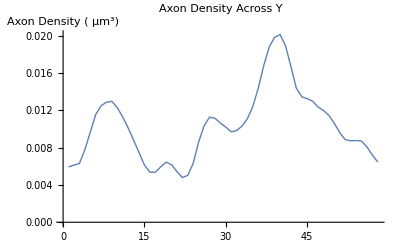

```mathematica
Show[ListPlot[window/(First[ImageDimensions[First[image]]]* Last[ImageDimensions[First[image]]]*3), Joined -> True, PlotStyle->Thick, PlotLabel-> "Axon Density Across Y",LabelStyle->Directive[Bold],  AxesLabel->"Axon Density ( µm^3)" ]]
```

## Author contact information

jej19@wra.net